# Diffusive Dynamics 2D Quick Start

Here we will generate a 2D diffusive trajectory and then analyze it.

## Load needed packages

```mathematica
(*Helps to free up memory*)
$HistoryLength=1;
(*Load the package*)
Needs["DiffusiveDynamics`"]
(*Load the package for parallel kernels as well*)
ParallelNeeds["DiffusiveDynamics`"]
ParallelEvaluate[$HistoryLength=1];
```

## Define diffusion parameters

```mathematica
(*The number of steps*)
STEPS=1000000;
(*The time step*)
STEP=1; 
(*The unit cell vectors (origin is at 0,0 and the size is from -1000 to 1000 in the x and -500 to 500 in the y dimension*)
CELLRANGE={1000.,500.}; 

(*For maximum speed the diffusion expression should be compiled*)
(*The diffusion is given as the major and minor axis of the diffusion tensor and the angle of rotation around the origin from the original x axis *)
DIFFX=Compile[{x,y},
5Sin[x/ CELLRANGE[[1]] π] +10];
DIFFY=Compile[{x,y},
5Sin[y/ CELLRANGE[[2]] π] +10];
ALPHA=Compile[{x,y},
(((x/2)/CELLRANGE[[1]])^2+((y/2)/ CELLRANGE[[2]])^2)*180];

(*Energy is in units of kT*)
KT=1;
(*Here as a simplest case energy is constant*)
ENERGY=Compile[{x,y},0];

(*Draw the diffusion components*)
CELL$plots=DiffusionParameters2DPlots[DIFFX,DIFFY,ALPHA,ENERGY,CELLRANGE];
CELL$label=StringForm["STEPS `1`; TIMESTEP `2`; KT `3`",STEPS,STEP,KT];
Labeled[CELL$label,CELL$plots]
```

STEPS 1000000; TIMESTEP 1; KT 1{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Generate the trajectory

```mathematica
(*Uses all available cores and by default generates 2*number of cores of segements. The total length off all segments is equal to STEPS. *)
rw=ParallelGenerateDiffusionTrajectory2D[STEPS,DIFFX,DIFFY,ALPHA,ENERGY,KT,STEP,{-CELLRANGE,CELLRANGE}];
```

Getting help

```mathematica
(*Additional help is avalable by using the question mark ? *)
?ParallelGenerateDiffusionTrajectory2D
```

ParallelGenerateDiffusionTrajectory2D[steps, DiffX, DiffY, DiffA, F, kT, dt, {min,max},opt]
Generates a 2D diffusive process where the difusion tensor and energy optionally depend on the location of the particle. 
Uses "ProcessCount" threads to generate  "ProcessCount" independent trajectories.

steps      -- number of steps to perform
DiffX[x,y] -- a Function or CompiledFunction giving the difusion in the X and Y principal direction
DiffY[x,y] -- as above for the Y direction
DiffA[x,y] -- a Function or CompiledFunction giving the rotation of the principal direction
F[x,y]     -- Free Energy as a function of position (must be either a Function or CompiledFunction)
kT         -- set the temparature in units of kT (thermal energy = boltzman konstant* temperature
dt         -- the time size of one step
min        -- the minimum sizes of the periodic cell {minX, minY}
max        -- the maximum sizes of the periodic cell {maxX, maxY}


OPTIONS:
"ProcessCount"-> 2$ProcessorCount -- Number of independent difussion processe that get started in seperate threads
"InitialPositions"->Automatic     -- takes a list of points or the default, Automatic, which generates uniformly randommly distributed points in the cell
"RandomSeeds"->Automatic          -- takes a list of random seeds used to generate each trajectory.
"Verbose"->False            -- Log output
"VerboseLevel"->3           -- Verbosity of the output  

See also GenerateDiffusionTrajectory2D for further info.

```mathematica
(*Options of any command can be obtained by.*)
Options[ParallelGenerateDiffusionTrajectory2D]
```

{ProcessCount:>2 $ProcessorCount,InitialPositions→Automatic,RandomSeeds→Automatic,RandomSeed→Automatic,InitialPosition→{0.,0.},Verbose:>$VerbosePrint,VerboseLevel:>$VerboseLevel}

```mathematica
(*To list all methods in a module the start * wild card can be used*)
?DiffusiveDynamics`Generate2D`*
```

Visualize the trajectory

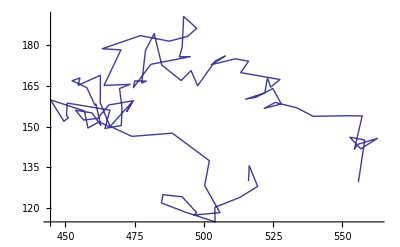

```mathematica
(*First a closer look at one trajectory*)
ListLinePlot[rw[[1,;;100,{2,3}]]]
```

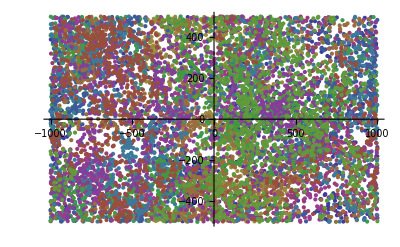

```mathematica
(*The points are approxmately uniformely distributed since energy is constatn*)
ListPlot[rw[[All,;;;;100,{2,3}]]]
```

## Analyze the trajectory

```mathematica
(*We have to decide on the number of bins (or eqvivalently the size of each bin) in each. Here we take 10 bins in each dimension*)
```

```mathematica
w=CELLRANGE/5;
binSpec=Transpose[{-CELLRANGE,CELLRANGE,w}];
(*we also have to decide what strides we would like. Strides basically adjust the sampling timescale to Stride*Timestep*)
STRIDES={1,10,100};
diffs=GetDiffusionInBins[rw,STEP,binSpec,"StepsToBinMethod"->"Pad","Strides"->STRIDES,"Parallel"->True];
```

GetDiffusionInBins returns a list of list of rules. The first dimension are the bins and the second the sampling timescales (strides).
The list of rules is (hopefully) self-explanatory. Dx and Dy are the diffusion tensor eigen values and Da the rotation origin form the original x axis to Dx. ux and uy are the averages of the distribution of steps, sx and sy the widths of the Gaussian distribution of steps. x and y are the bin centers, xWidth and yWidth the widths of the bin. xMinWidth and yMinWidth are minimum widths of the bin necessary to include all steps. This should in general be smaller than xWidth and yWidth. dt is the time-step and Stride determines the sampling timescale by dt*Stride. Steps in bin is the number of steps sampled in this bin.

```mathematica
Dimensions@diffs
diffs[[50,3]] (*Fiftieth bin, second stride*)
```

{100,3,19}

{Dx→13.5145,Dy→9.43114,Da→105.413,ux→-0.293118,uy→0.12244,sx→51.9893,sy→43.4307,PValue→0.89346,IsNormal→True,xMinWidth→251.212,yMinWidth→251.212,Stride→100,x→-100.,y→450.,xWidth→200.,yWidth→100.,StepsInBin→269,dt→1,StepsHistogram→Null}

Get the model diffusion as well

```mathematica
modelDiffs=GetDiffusionInfoFromParameters[binSpec,STEP,STRIDES,DIFFX,DIFFY,ALPHA,"Parallel"->True];
First@modelDiffs;
```

## Visualize the result

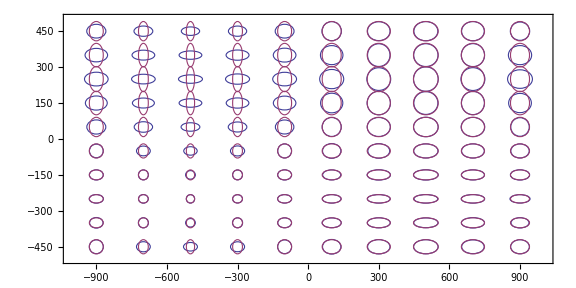

```mathematica
(*We see almost perfect aligment at stride 1*)
DrawDiffusionTensorRepresentations[{diffs[[All,1]], modelDiffs[[All,1]]},1(*this 1 is the selected bin*),Scale->3.5,ImageSize->Large]
```

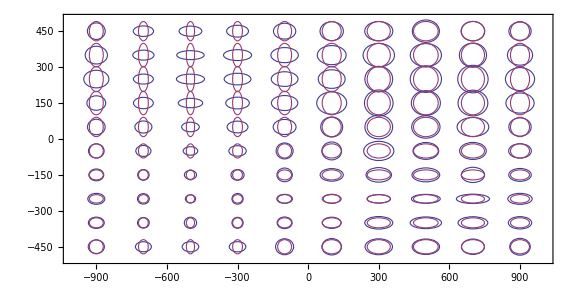

```mathematica
(*We see almost perfect aligment at stride 100 there are small diffrences, due to less sampled steps*)
DrawDiffusionTensorRepresentations[{diffs[[All,3 ]], modelDiffs[[All,3]]},1,Scale->3.5,ImageSize->Large]
```

The plot can be tweaked for publication quality display

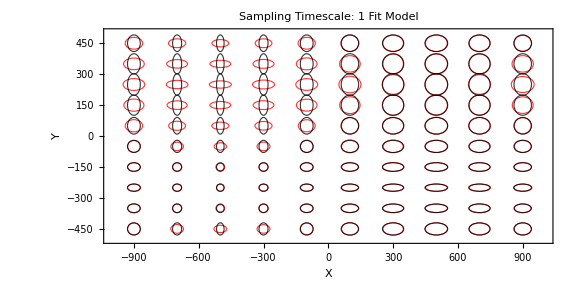

```mathematica
s=1;
DrawDiffusionTensorRepresentations[{diffs[[All,s]], modelDiffs[[All,s]]},1
,Scale->3.5,ImageSize->Large
,PlotLabel->Row@{"Sampling Timescale: ",s*STEP,"\n",Style[" Fit ",Red],"Model"}
,PlotStyle->{Directive[Thick,Red,Opacity@.8],Directive[Thin,Black,Opacity@.8]}
,LabelStyle->{14,Bold,FontFamily->"Arial"}
,FrameLabel->{"X","Y"}, Axes->False
]
```

The full power of Mathematica and manipulate can be leveraged

```mathematica
Manipulate[

DrawDiffusionTensorRepresentations[{diffs[[All,s]], modelDiffs[[All,s]]},1
,Scale->3.5,ImageSize->Large
,PlotLabel->"Sampling Timescale: "<>ToString[s*STEP]
,PlotStyle->{Directive[Thick,Red,Opacity@.6],Directive[Thick,Black,Opacity@.6]}
,LabelStyle->{14,FontFamily->"Arial"}
,FrameLabel->{"X","Y"}]

,
{s,1,Length@STRIDES,1}]
```

The diffusion can be compared interactively

```mathematica
ViewDiffsWithStridePlots[{diffs,modelDiffs},"Comparison Fitted/Model",SaveDefinitions->False,Verbose->False]
```